```mathematica
SetDirectory[NotebookDirectory[]];
<<MeshTools.wl
```

```mathematica
bmesh=BoundaryElementMeshJoin[ToBoundaryMesh[Annulus[{0,0},{1,1.5}],"BoundaryMarkerFunction"->Function[{coords,points},If[Norm[#//Mean]>1,5,6]&/@coords]],ToBoundaryMesh[Rectangle[{-3,-3},{3,3}]]];
air={{0,0},{0,2}};
dielectric={0,1.25};
mesh=ToElementMeshDefault[bmesh,Append[{#,1}&/@air,{dielectric,2}]];
```

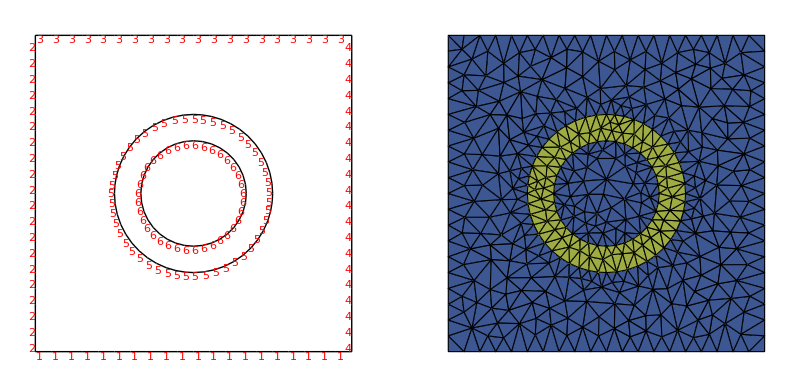

```mathematica
MeshInspect[mesh]
```

```mathematica
SolutionDirectory="solutions/";
```

```mathematica
InterpAndShow[Import[SolutionDirectory<>"annulus_dielectric.txt","Data"],Annulus[{0,0},{1,1.5}]]
```

-Graphics-